```mathematica
FName[name_,p_,q_,d_]:=NotebookDirectory[]<>name<>"_"<>ToString[p]<>"_"<>ToString[q]<>If[d>=p+q,"","_"<>ToString[d]];
irrepDims[p_,q_,d_]:=irrepDims[p,q,d]= Import[FName["idempotents/metadata",p,q,d]<>".m"][[1]];
```

```mathematica
(* Transpose a Brauer diagram *)
BT[σ_]:=SortB[B[Sequence@@(FlipPair[#,0]&/@(σ/.B->List))]];
(* Sort the diagram description to make it canonical *)
SortB[σ_]:=Sort@Map[Sort,σ,1];
(*Given the line defined by a pair of vertices, flip the vertices which are located after the wall at level p*)
FlipPair[pair_,p_]:=Sort@(If[Abs[#]>p,-#,#]&/@pair);
(*Generate Walled Brauer Algebra generators*)
WalledBrauerGenerators[p_,q_]:=WalledBrauerGenerators[p,q]=B[Sequence@@#]&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Table[Range[i-1]~Join~{i+1,i}~Join~Range[i+2,p+q],{i,1,p+q-1}],{2}];
(*Generate Walled Brauer Algebra basis*)
WalledBrauerBasis[p_,q_]:=WalledBrauerBasis[p,q]=(SortB[B[Sequence@@#]])&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Permutations[Range[p+q]],{2}];
```

```mathematica
(* Contract a Brauer diagram at one fixed position l *)
ContractDiag[diag__,{l_,d_}]:=Module[{new,data},
data=diag/.B->List;
new=Sort@Flatten@Table[If[data[[i]]∩{-l,l}!={},Complement[data[[i]],{-l,l}],{}],{i,1,Length@data}];
If[new=={},d SortB[B[Sequence@@Sort@Table[If[data[[i]]∩{-l,l}!={},Nothing,data[[i]]],{i,1,Length@data}]]], SortB[B[Sequence@@Sort@(Table[If[data[[i]]∩{-l,l}!={},Nothing,data[[i]]],{i,1,Length@data}]~Join~{new})]]]
];
(* Contract a lin. comb. of Brauer diagrams x at one fixed position l *)
ContractOne[x_,{l_,d_}]:=x/.B[lst__]:>ContractDiag[{lst},{l,d}];
(* Contract a lin. comb. of Brauer diagrams x at fixed positions lst *)
Contract[x_,lst_List,d_]:=Fold[ContractOne,x,{lst,ConstantArray[d,Length@lst]}ᵀ];
(* Compute the full trace of a lin. comb. of Brauer diagrams x *)
FullContract[x_,p_,q_,d_]:=Contract[x,Table[i,{i,p+q}],d]/.B[]->1;
(* Same functions, but for 2 registers *)
ContractOne2[x_,{l_,d_}]:=If[l>=p+q+1,x/.(B[lst1__]⊗B[lst2__]:>B[lst1]⊗ContractDiag[{lst2},{l-p+q,d}]),x/.(B[lst1__]⊗B[lst2__]:>ContractDiag[{lst1},{l,d}]⊗B[lst2])];
Contract2[x_,lst_List,d_]:=Fold[ContractOne2,x,{lst,ConstantArray[d,Length@lst]}ᵀ]/.B[]->1;
FullContract2[x_,p_,q_,d_]:=FullContract[Contract2[x,Range[(p+q)],d]/.B[]->1,d];
```

```mathematica
(* Multiply two Brauer algebra diagrams *)
MultiplyPair2[σ1_,σ2_,d_]:=Module[{lst,i,new,pos,σ1n,σ2n},
σ1n=Map[If[#<0,Subscript[b, -#],Subscript[a, #]]&,List@@σ1,{2}];
σ2n=Map[If[#<0,Subscript[b, -#],Subscript[a, #]]&,List@@σ2,{2}];
(* Denote the nodes in the middle layer by x *)
lst=Join[σ1n/.b->x,σ2n/.a->x];
(* Treat each node Subscript[x, i] in the intermediate level *)
Do[
(* Find all edges containing Subscript[x, i] *)
new=lst⟦pos=Position[lst,Subscript[x, i],{2}]⟦All,1⟧⟧;
(* Update the list by removing these edges and adding a new one *)
lst=Append[Delete[lst,List/@pos],DeleteCases[Join@@new,Subscript[x, i]]];
,{i,1,Length[σ1]}
];
(* Output the new Brauer diagram and the normalization factor from the number of loops *)
{B@@SortB@Map[If[TrueQ[First[#]==b],-Part[#,2],Part[#,2]]&,DeleteCases[lst,{}],{2}],d^Count[lst,{}]}
];
(* Multiply two Brauer algebra diagrams *)
MultiplyPair[σ1_,σ2_,d_]:=Times@@MultiplyPair2[σ1,σ2,d];
```

```mathematica
(* Convert integer to a string and padd with 0s *)
Str[i_,max_]:=StringJoin@@(ToString/@IntegerDigits[i,10,IntegerLength@max]);
(* Shorter variable names that also account for symmetry *)
x[λ_,μ_,i_,j_,k_,l_,dB_]:=Symbol["x"<>Str[λ,Length@dB]<>Str[μ,Length@dB]<>StringJoin@@Sort[{Str[i,dB⟦λ⟧]<>Str[k,dB⟦μ⟧],Str[j,dB⟦λ⟧]<>Str[l,dB⟦μ⟧]}]];
```

```mathematica
(* Diagram multiplication tensor *)
prodRule[p_,q_,d_,i_,j_]:=Block[{basis=WalledBrauerBasis[p,q],prod},prod=MultiplyPair2[basis[[i]],basis[[j]],d];{i,j,Position[basis,prod[[1]]][[1,1]]}->prod[[2]]];
mulTensor[p_,q_,d_]:=mulTensor[p,q,d]=SparseArray[Flatten@Table[prodRule[p,q,d,i,j],{i,1,(p+q)!},{j,1,(p+q)!}],{(p+q)!,(p+q)!,(p+q)!}];

(* Diagram contraction tensor *)
contractTensor[p_,q_,d_]:=contractTensor[p,q,d]=Table[FullContract[WalledBrauerBasis[p,q][[i]],p,q,d],{i,1,(p+q)!}];
contractTensor[p_,q_,d_,lst_]:=contractTensor[p,q,d,lst]=Table[(Contract[WalledBrauerBasis[p,q][[i]],lst,d]/.{(B[y__]:>B[Sequence@@({y}/.Flatten[{#[[1]]->#[[2]],-#[[1]]->-#[[2]]}&/@({Complement[Range[p+q],lst],Range[p+q-Length[lst]]}ᵀ)])])})
/.{B[]:>1,B[arg__]:>SparseArray[{Position[WalledBrauerBasis[p-Count[lst,x_/;x<=p],q-Count[lst,x_/;x>p]],B[arg],{1}][[1,1]]}->1,(p+q-Length[lst])!]},{i,1,(p+q)!}]ᵀ;

(* Diagram contraction and adding Id tensor *)
contractIdTensor[p_,q_,d_,lstContract_,lstId_]:=contractIdTensor[p,q,d,lstContract,lstId]=Table[(Contract[WalledBrauerBasis[p,q][[i]],lstContract,d]/.(B[y___]:>SortB@B[Sequence@@({y,Sequence@@({-#,#}&/@lstId)}/.Flatten[{#[[1]]->#[[2]],-#[[1]]->-#[[2]]}&/@({Complement[Range[p+q],Complement[lstContract,lstId]],Range[p+q-Length[lstContract]+Length[lstId]]}ᵀ)])]))/.
{B[]:>1,B[arg__]:>SparseArray[{Position[WalledBrauerBasis[p-Count[Complement[lstContract,lstId],x_/;x<=p],q-Count[Complement[lstContract,lstId],x_/;x>p]],B[arg],{1}][[1,1]]}->1,(p+q-Length[lstContract]+Length[lstId])!]}
,{i,1,(p+q)!}]ᵀ

(* Auxilary tensors *)
mulTensorMatrix[p_,q_,d_]:=mulTensorMatrix[p,q,d]=Flatten[mulTensor[p,q,d],{{1,2},{3}}];
MulContractTensor[p_,q_,d_]:=MulContractTensor[p,q,d]=ArrayReshape[mulTensorMatrix[p,q,d].contractTensor[p,q,d],{(p+q)!,(p+q)!}]
```

```mathematica
(* Operations od 1vecs *)
FullContractVec[vec_,p_,q_,d_]:=(contractTensor[p,q,d].{vec}ᵀ)[[1]]
MultiplyVecs[vec1_,vec2_,p_,q_,d_]:=Flatten[KroneckerProduct[vec1,vec2]].mulTensorMatrix[p,q,d]
MultiplyVecs[vec1_,vec2_,vec3_,p_,q_,d_]:=MultiplyVecs[vec1,MultiplyVecs[vec2,vec3,p,q,d],p,q,d]

(*Define psd constraints and make them symmetric*)
psd[λ_,μ_,p_,q_,d_]:=psd[λ,μ,p,q,d]=Flatten[Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}],{{1,2},{3,4}}];

(*Contract vec, which has the form ∑KroneckerProduct[*,*] on given list of indices *)
Contract2Vec[vec_,p_,q_,d_,lst_]:=contractTensor[q,p,d,Select[lst,#<=(p+q)&]].vec.contractTensor[p,q,d,Select[lst,#>(p+q)&]-(p+q)]ᵀ
Contract2Vec[vec_,p_,q_,d_]:=Contract2Vec[vec,p,q,d,Range[2(p+q)]]
```

```mathematica
(* Realise linear constraints *)
Psys[p_,q_]:={1};
Osys[p_,q_]:=Range[2,p+q];
Isys[p_,q_]:=Range[p+q+1,2(p+q)-1];
Fsys[p_,q_]:={2(p+q)};

Choi[ansatz_,i_,p_,q_,d_]:=If[i<p+q,Expand[If[i==0,Contract2Vec[ansatz,p,q,d],Contract2Vec[ansatz,p,q,d,Osys[p,q][[i;;p+q-1]]~Join~Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q]]]/d^(p+q-i)],ansatz]

TrChoi[ansatz_,i_,p_,q_,d_]:=If[i==0,Print["Error: i should be >0"],Expand[Contract2Vec[ansatz,p,q,d,Osys[p,q][[i;;p+q-1]]~Join~Isys[p,q][[i;;p+q-1]]~Join~Fsys[p,q]]/d^(p+q-i)]]

ChoiTensorId[ansatz_,i_,p_,q_,d_]:=Expand[If[i>=1,
contractIdTensor[q,p,d,Osys[p,q][[i;;p+q-1]],Osys[p,q][[i;;i]]].ansatz.contractTensor[p,q,d,(Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q])-(p+q)]ᵀ,
contractIdTensor[q,p,d,Osys[p,q]~Join~Psys[p,q],Psys[p,q]].ansatz.contractTensor[p,q,d,(Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q])-(p+q)]ᵀ
]/d^(p+q-i)]
```

```mathematica
(* Load blocks *)
ClearAll[blocksLoad,blocksLoadN]
blocksLoad[p_,q_,d_]:=blocksLoad[p,q,d]=Import[FName["blocks/blocks",p,q,d]<>".m"]
blocksLoadN[p_,q_,d_,prec_]:=blocksLoadN[p,q,d,prec]=N[blocksLoad[p,q,d],prec]

(* Map 2vec to selected blocks *)
vec2ToBlocks[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Sum[vec[[i,j]]KroneckerProduct[blocksLoad[pλ,qλ,d][[i,λ]],blocksLoad[pμ,qμ,d][[j,μ]]],{i,1,(pλ+qλ)!},{j,1,(pμ+qμ)!}]
vec2ToBlocksN[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_,prec_]:=Sum[vec[[i,j]]KroneckerProduct[blocksLoadN[pλ,qλ,d,prec][[i,λ]],blocksLoadN[pμ,qμ,d,prec][[j,μ]]],{i,1,(pλ+qλ)!},{j,1,(pμ+qμ)!}]

(* Map 2vec to selected blocks *)
vec2ToBlocksBetter[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Flatten[vec].Flatten[Outer[KroneckerProduct,blocksLoad[pλ,qλ,d][[All,λ]],blocksLoad[pμ,qμ,d][[All,μ]],1],{{1,2},{3},{4}}]
vec2ToBlocksBetterN[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_,prec_]:=Flatten[vec].Flatten[Outer[KroneckerProduct,blocksLoadN[pλ,qλ,d,prec][[All,λ]],blocksLoadN[pμ,qμ,d,prec][[All,μ]],1],{{1,2},{3},{4}}]
```

```mathematica
cyclicDiag[n_]:=cyclicDiag[n]=SortB[B[Sequence@@(FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,PermutationList[Cycles[{Range[n]}]],Range[n]][[-1]])]];
shiftTensor[p_,q_,d_]:=SparseArray[Table[{i,Position[WalledBrauerBasis[q,p],MultiplyPair[cyclicDiag[p+q],MultiplyPair[WalledBrauerBasis[p,q][[i]],BT@cyclicDiag[p+q],d],d]][[1,1]]}->1,{i,1,(p+q)!}],{(p+q)!,(p+q)!}]
shiftVec[vec_,p_,q_,d_]:=vec.shiftTensor[p,q,d]
```

```mathematica
{p,q,d}={3,0,2};
Print["{p, q, d} = ",{p,q,d}]
Print["Dimensions of simple (𝒜^d)_(p, q)-modules = ",irrepDims[p,q,d]]
```

{p, q, d} = {3,0,2}

Dimensions of simple (𝒜^d)_(p, q)-modules = {1,2}

```mathematica
ε=Import[FName["idempotents/elementary",p,q,d]<>".m"];
εLeft=Import[FName["idempotents/elementary",q,p,d]<>".m"];
{ε,εLeft}=N[{ε,εLeft},50];
dimλU=Table[FullContractVec[ε[[λ,1,1]],p,q,d],{λ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
dimλU
```

{4.,2.}

```mathematica
indices=Flatten[Table[{λ,μ,i,j,k,l},{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}],5];
Length@indices
chunks=Partition[indices,UpTo@100];
X[{λ_,μ_,i_,j_,k_,l_}]:=(x[λ,μ,i,j,k,l,irrepDims[p,q,d]])KroneckerProduct[εLeft[[λ,i,j]],ε[[μ,k,l]]];
Timing[ansatz=Sum[Sum[X[m],{m,chunks⟦i⟧}],{i,Length@chunks}];]
```

1764

{17.9961,Null}

```mathematica
Timing[Export[FName["app4_data/ansatz",p,q,d]<>"_50_left.m",ansatz];]
```

{79.6505,Null}

```mathematica
(*Generate the ansatz via eq. (13) in arXiv:2209.02907*)
ansatz=Expand@ParallelSum[(x[λ,μ,i,j,k,l,irrepDims[p,q,d]])KroneckerProduct[εLeft[[λ,i,j]],ε[[μ,k,l]]],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
```

```mathematica
ansatz//MatrixForm;
ansatzNumeric=N[ansatz,50];
```

```mathematica
ansatzNumeric=ansatz;
```

```mathematica
Export[FName["app4_data/ansatz",p,q,d]<>".m",N@ansatz]
```

```mathematica
(*(*Load the above ansatz from the memory*)
ansatz=Import[NotebookDirectory[]<>"app4_data/ansatz_normal_"<>ToString[p]<>"_"<>ToString[q]<>"_"<>ToString[d]<>".m"]/.symSol[p,q,d];*)
```

```mathematica
ansatzNumeric=ansatz;
```

```mathematica
ansatzNumeric=Import[FName["app4_data/ansatz",p,q,d]<>".m"];
```

```mathematica
(*Generate the matrix Ω from eq. (18) in arXiv:2209.02907 *)
Ω=Sum[1/d^2 1/dimλU[[λ]] KroneckerProduct[εLeft[[λ,i,j]],shiftVec[ε[[λ,i,j]],p,q,d]],{λ,1,Length[irrepDims[p,q,d]]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧}];
```

```mathematica
Timing[M=MulContractTensor[p,q,d].Ω.MulContractTensor[p,q,d];]
Timing[objective=Chop@Total@Expand[Flatten[Mᵀ]*Flatten[ansatzNumeric]];]
```

{2.08158,Null}

{11.3804,Null}

```mathematica
mulTensorMatrix[p,q,d]==mulTensorMatrix[q,p,d]
```

False

```mathematica
objective/.x__Real:>RootApproximant[x];
```

```mathematica
eqConstrRaw=Table[PrintTemporary[i];Chop[TrChoi[ansatzNumeric,i,p,q,d]-ChoiTensorId[ansatzNumeric,i-1,p,q,d]],{i,1,p+q}];
```

```mathematica
Timing[eqConstr=Chop@Flatten[{Choi[ansatzNumeric,0,p,q,d]-1}~Join~eqConstrRaw[[1;;2]]~Join~Table[PrintTemporary[i];Table[PrintTemporary[{λ,μ,irrepDims[q,i-q,d]⟦λ⟧*irrepDims[i-1,0,d]⟦μ⟧}];Expand@vec2ToBlocksBetterN[eqConstrRaw[[i]],λ,μ,q,i-q,i-1,0,d,50],{λ,1,Length[irrepDims[q,i-q,d]]},{μ,1,Length[irrepDims[i-1,0,d]]}],{i,3,p+q}]];]
```

{160.841,Null}

```mathematica
Export[FName["app4_data/eq",p,q,d]<>"_50_left.m",eqConstr]
```

```mathematica
eqConstr/.x__Real:>RootApproximant[x];
```

$Aborted

```mathematica
eqConstr=Import[FName["app4_data/eq",p,q,d]<>"_50_left.m"];
```

```mathematica
eqConstrExact=Import[FName["app4_data/eq",p,q,d]<>"_exact.m"];
```

```mathematica
eqConstrExact/.guessAnsatz//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Solve[(#==0)&/@Union@FullSimplify@Union@(eqConstrExact/.guessAnsatz)]
```

{{a1→-(√5)/4,a2→(√(3/2))/2,a3→-1/(2 √2),a4→-1/(2 √6),a5→-1/(4 √3)}}

```mathematica
(***************************************)
```

```mathematica
elim={};
```

```mathematica
elim=zeroes;
```

```mathematica
psdElim[λ_,μ_,p_,q_,d_]:=Chop@Expand[psd[λ,μ,p,q,d]/.elim];
```

```mathematica
psdConstr=Flatten@Table[VectorGreaterEqual[{psdElim[λ,μ,p,q,d],0},{"SemidefiniteCone",irrepDims[p,q,d]⟦λ⟧*irrepDims[p,q,d]⟦μ⟧ }],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
vars=Variables@Table[psdElim[λ,μ,p,q,d],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
Length@%
```

932

```mathematica
(*~Join~((#==0)&/@{x311111,x311121,x311131,x311141,x311151,x311121,x312121,x312131,x312141,x312151,x311131,x312131,x313131,x313141,x313151,x311141,x312141,x313141,x314141,x314151,x311151,x312151,x313151,x314151,x315151})*)
```

```mathematica
sol=Dispatch@SemidefiniteOptimization[-objective/.elim,psdConstr~Join~((#==0)&/@(eqConstr/.elim))~Join~{x333131==0,x232121==0,x231414==0,x333434==0,x231111==0},vars];
```

SemidefiniteOptimization::parsuc: Partial Success; a solution has been found, but full accuracy was not achieved. One or more of primal infeasibility, dual infeasibility, or relative duality gap are larger than their tolerances, but by a factor of less than 1000. Specifying a value for MaxIterations greater than 100 may improve the solution.

```mathematica
objective/.sol/.elim//Chop
```

1.9438

```mathematica
Sort@Abs@Chop[vars/.sol,10^-3]
Length@%
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00100506,0.00100944,0.00101186,0.00101627,0.00112283,0.00117245,0.00120896,0.00121239,0.0012136,0.00121741,0.00140815,0.00141885,0.00147449,0.00157947,0.00158605,0.00172302,0.00172602,0.00173261,0.00173432,0.00173589,0.00173992,0.00197381,0.00198201,0.00198881,0.00199697,0.125234,0.249495,0.249981,0.249981,0.249981,0.491785,0.491785,0.49294,0.494106,0.494106,0.494701,0.495256,0.495272,0.496446,0.496446,0.497023,0.497602,0.499365}

932

```mathematica
Sort@Abs@Chop[vars/.sol,10^-5]
Length@%
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00925925,0.00925925,0.0130946,0.0130946,0.0160374,0.0160374,0.0166511,0.0185185,0.0226804,0.0226805,0.0226805,0.0261891,0.0261891,0.0261891,0.0262966,0.0277775,0.027804,0.0288404,0.0320751,0.037037,0.037037,0.037037,0.037037,0.0392836,0.0453607,0.0453607,0.0481125,0.0481125,0.0481579,0.049953,0.0523783,0.0554416,0.0555558,0.0641498,0.0641501,0.0641502,0.0680414,0.074074,0.074074,0.0833326,0.083333,0.0834118,0.0907221,0.0926306,0.104757,0.104757,0.117851,0.136083,0.136083,0.144337,0.144337,0.148148,0.156813,0.157711,0.166866,0.19245,0.249999,0.25,0.25,0.25,0.25,0.433012,0.433013,0.443533,0.499402,0.75}

116

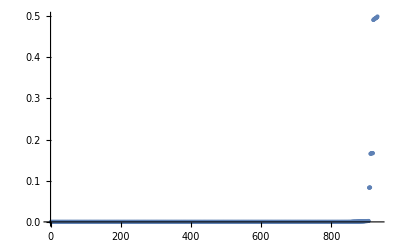

```mathematica
Abs@Chop[vars/.sol,10^-5];
ListPlot@Sort@%
```

```mathematica
Flatten@Position[Chop[vars/.sol,10^-4],0];
zeroes=Rule@@@Transpose@{vars⟦%⟧,ConstantArray[0,Length@%]};
```

```mathematica
zeroes=Union@Join[zeroes,zeroes2];
```

```mathematica
(* Guess for blocks p=4, q=1 *)
(*Block 2,3*)
v[2,3]=({{0, 0, 0, -(√15)/12, -(√5)/4, 0, 0, 0, (√(3/2))/2, -1/(2 √2), 0, 0, 0, -1/(6 √2), -1/(2 √6), 0, 0, 0, -1/12, -1/(4 √3)}, {(√15)/12, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(8 √2)/12, 0, 0, 0, 0, 1/12, 0, 0, 0, 0}, {0, 0, 0, -1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√15)/4, 0}, {0, 0, 0, (√15)/12, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(2 √2)/3, 0, 0, 0, 0, 1/12, 0}, {1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(√15)/4, 0, 0, 0, 0}});
λs[2,3]={1,1/6,1/6,1/6,1/6};
B[2,3]=v[2,3]ᵀ.DiagonalMatrix[λs[2,3]].v[2,3]//FullSimplify;
(*Block 3,3*)
v[3,3]=({{3/8, (√3)/8, 0, (√3)/8, -1/8, -(√3)/8, 3/8, 0, 1/24, 1/(8 √3), 0, 0, 0, -1/(3 √2), -1/(√6), -(√3)/8, -1/8, 0, 3/8, -(√3)/8, -1/8, (√3)/8, 0, -1/(8 √3), -1/8}, {0, 0, 0, 0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0}, {0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0, 0, 0, 0}});
λs[3,3]={2,1/6,1/6};
B[3,3]=v[3,3]ᵀ.DiagonalMatrix[λs[3,3]].v[3,3]//FullSimplify;
(*Block 2,2*)
v[2,2]=({{0, -1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√15)/4, 0, 0}, {0, -(√(5/3))/4, 0, 0, 0, 0, 0, 0, 0, (2 √2)/3, 0, 0, 0, -1/12, 0, 0}});
λs[2,2]={1/12,1/12};
B[2,2]=v[2,2]ᵀ.DiagonalMatrix[λs[2,2]].v[2,2]//FullSimplify;
(*Block 3,2*)
v[3,2]=({{0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0, 0}});
λs[3,2]={1/12};
B[3,2]=v[3,2]ᵀ.DiagonalMatrix[λs[3,2]].v[3,2]//FullSimplify;
B[1,1]=ConstantArray[0,{1,1}];
B[2,1]=ConstantArray[0,{4,4}];
B[3,1]=ConstantArray[0,{5,5}];
B[1,2]= ({{0, 0, 0, 0}, {0, 1/12, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
B[1,3]= ({{1/6, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 1/6, 0}, {0, 0, 0, 0, 0}});
```

```mathematica
guessAnsatz=Dispatch@Flatten@Table[Rule@@@Transpose@{Flatten[Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}]],Flatten[B[λ,μ]]},{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
blocks=Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]]/.elim/.sol,{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
blocks=Flatten[Chop[blocks,10^-4],{{1},{2},{3,4},{5,6}}];
MatrixForm@Map[MatrixForm,blocks,{2}]
```

((0) | (0 | 0 | 0 | 0
0 | 0.125234 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0.249495 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.249981 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.249981 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00173261 | 0 | 0 | -0.00158605 | 0 | 0.00172602 | 0.00121741
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00158605 | 0 | 0 | 0.00147449 | 0 | -0.00157947 | -0.00112283
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00172602 | 0 | 0 | -0.00157947 | 0 | 0.00172302 | 0.00121239
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00121741 | 0 | 0 | -0.00112283 | 0 | 0.00121239 | 0.000865032) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.496446 | 0 | 0 | 0 | 0 | 0 | 0.494106
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.494106 | 0 | 0 | 0 | 0 | 0 | 0.491785)
(0 | 0 | 0 | 0 | 0
0 | 0.000393955 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.000491646) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.00029695 | 0 | 0 | 0 | 0 | -0.000293449 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000508133 | 0 | 0 | 0 | 0 | 0.000505928 | 0.000360954
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.000586451 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.000293449 | 0 | 0 | 0 | 0 | 0.000293369 | 0 | 0 | 0 | 0 | 0 | 0 | -0.000504721 | 0 | 0 | 0 | 0 | -0.000502531 | -0.000358523
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000586276 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.249981 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.000508133 | 0 | 0 | 0 | 0 | -0.000504721 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000887836 | 0 | 0 | 0 | 0 | 0.000884504 | 0.000619216
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000738109 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.000505928 | 0 | 0 | 0 | 0 | -0.000502531 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000884504 | 0 | 0 | 0 | 0 | 0.00088473 | 0.000616506
0 | 0.000360954 | 0 | 0 | 0 | 0 | -0.000358523 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000619216 | 0 | 0 | 0 | 0 | 0.000616506 | 0.00044146) | (0.499365 | 0 | 0 | 0 | 0 | 0 | 0.497023 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00101627 | 0 | 0 | -0.497602 | 0 | 0 | 0.00101186 | 0.000721907 | 0 | -0.495256
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.497023 | 0 | 0 | 0 | 0 | 0 | 0.494701 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00100944 | 0 | 0 | -0.495272 | 0 | 0 | 0.00100506 | 0.000717046 | 0 | -0.49294
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00117245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00101627 | 0 | 0 | 0 | 0 | 0 | -0.00100944 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00173992 | 0 | 0 | 0.00199697 | 0 | 0 | -0.00173432 | -0.0012136 | 0 | 0.00198201
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.497602 | 0 | 0 | 0 | 0 | 0 | -0.495272 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00199697 | 0 | 0 | 0.496446 | 0 | 0 | -0.00198881 | -0.00141885 | 0 | 0.494106
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00101186 | 0 | 0 | 0 | 0 | 0 | 0.00100506 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00173432 | 0 | 0 | -0.00198881 | 0 | 0 | 0.00173589 | 0.00120896 | 0 | -0.00197381
0.000721907 | 0 | 0 | 0 | 0 | 0 | 0.000717046 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0012136 | 0 | 0 | -0.00141885 | 0 | 0 | 0.00120896 | 0.000865697 | 0 | -0.00140815
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.495256 | 0 | 0 | 0 | 0 | 0 | -0.49294 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00198201 | 0 | 0 | 0.494106 | 0 | 0 | -0.00197381 | -0.00140815 | 0 | 0.491785))

```mathematica
(**)
```

((0) | (0 | 0 | 0
0 | 0.16693 | 0
0 | 0 | 0) | (0.49921 | 0
0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.166975 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.333333 | 0 | -0.272166 | 0 | 0.19245
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.272166 | 0 | 0.222223 | 0 | -0.157135
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.19245 | 0 | -0.157135 | 0 | 0.111111) | (0.499076 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)
(0 | 0
0 | 0.0665944) | (0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.111232 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0) | (1. | 0 | 0 | 0.57735
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0.57735 | 0 | 0 | 0.333332))

```mathematica
blocks=Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]]/.elim,{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
blocks=Flatten[Chop[blocks,10^-4],{{1},{2},{3,4},{5,6}}];
MatrixForm@Map[MatrixForm,blocks,{2}]
```

((x111111) | (x121111 | x121112 | x121113 | x121114
x121112 | x121212 | x121213 | x121214
x121113 | x121213 | x121313 | x121314
x121114 | x121214 | x121314 | x121414) | (x131111 | x131112 | x131113 | x131114 | x131115
x131112 | x131212 | x131213 | x131214 | x131215
x131113 | x131213 | x131313 | x131314 | x131315
x131114 | x131214 | x131314 | x131414 | x131415
x131115 | x131215 | x131315 | x131415 | x131515)
(x211111 | x211121 | x211131 | x211141
x211121 | x212121 | x212131 | x212141
x211131 | x212131 | x213131 | x213141
x211141 | x212141 | x213141 | x214141) | (x221111 | x221112 | x221113 | x221114 | x221121 | x221122 | x221123 | x221124 | x221131 | x221132 | x221133 | x221134 | x221141 | x221142 | x221143 | x221144
x221112 | x221212 | x221213 | x221214 | x221221 | x221222 | x221223 | x221224 | x221231 | x221232 | x221233 | x221234 | x221241 | x221242 | x221243 | x221244
x221113 | x221213 | x221313 | x221314 | x221321 | x221322 | x221323 | x221324 | x221331 | x221332 | x221333 | x221334 | x221341 | x221342 | x221343 | x221344
x221114 | x221214 | x221314 | x221414 | x221421 | x221422 | x221423 | x221424 | x221431 | x221432 | x221433 | x221434 | x221441 | x221442 | x221443 | x221444
x221121 | x221221 | x221321 | x221421 | x222121 | x222122 | x222123 | x222124 | x222131 | x222132 | x222133 | x222134 | x222141 | x222142 | x222143 | x222144
x221122 | x221222 | x221322 | x221422 | x222122 | x222222 | x222223 | x222224 | x222231 | x222232 | x222233 | x222234 | x222241 | x222242 | x222243 | x222244
x221123 | x221223 | x221323 | x221423 | x222123 | x222223 | x222323 | x222324 | x222331 | x222332 | x222333 | x222334 | x222341 | x222342 | x222343 | x222344
x221124 | x221224 | x221324 | x221424 | x222124 | x222224 | x222324 | x222424 | x222431 | x222432 | x222433 | x222434 | x222441 | x222442 | x222443 | x222444
x221131 | x221231 | x221331 | x221431 | x222131 | x222231 | x222331 | x222431 | x223131 | x223132 | x223133 | x223134 | x223141 | x223142 | x223143 | x223144
x221132 | x221232 | x221332 | x221432 | x222132 | x222232 | x222332 | x222432 | x223132 | x223232 | x223233 | x223234 | x223241 | x223242 | x223243 | x223244
x221133 | x221233 | x221333 | x221433 | x222133 | x222233 | x222333 | x222433 | x223133 | x223233 | x223333 | x223334 | x223341 | x223342 | x223343 | x223344
x221134 | x221234 | x221334 | x221434 | x222134 | x222234 | x222334 | x222434 | x223134 | x223234 | x223334 | x223434 | x223441 | x223442 | x223443 | x223444
x221141 | x221241 | x221341 | x221441 | x222141 | x222241 | x222341 | x222441 | x223141 | x223241 | x223341 | x223441 | x224141 | x224142 | x224143 | x224144
x221142 | x221242 | x221342 | x221442 | x222142 | x222242 | x222342 | x222442 | x223142 | x223242 | x223342 | x223442 | x224142 | x224242 | x224243 | x224244
x221143 | x221243 | x221343 | x221443 | x222143 | x222243 | x222343 | x222443 | x223143 | x223243 | x223343 | x223443 | x224143 | x224243 | x224343 | x224344
x221144 | x221244 | x221344 | x221444 | x222144 | x222244 | x222344 | x222444 | x223144 | x223244 | x223344 | x223444 | x224144 | x224244 | x224344 | x224444) | (x231111 | x231112 | x231113 | x231114 | x231115 | x231121 | x231122 | x231123 | x231124 | x231125 | x231131 | x231132 | x231133 | x231134 | x231135 | x231141 | x231142 | x231143 | x231144 | x231145
x231112 | x231212 | x231213 | x231214 | x231215 | x231221 | x231222 | x231223 | x231224 | x231225 | x231231 | x231232 | x231233 | x231234 | x231235 | x231241 | x231242 | x231243 | x231244 | x231245
x231113 | x231213 | x231313 | x231314 | x231315 | x231321 | x231322 | x231323 | x231324 | x231325 | x231331 | x231332 | x231333 | x231334 | x231335 | x231341 | x231342 | x231343 | x231344 | x231345
x231114 | x231214 | x231314 | x231414 | x231415 | x231421 | x231422 | x231423 | x231424 | x231425 | x231431 | x231432 | x231433 | x231434 | x231435 | x231441 | x231442 | x231443 | x231444 | x231445
x231115 | x231215 | x231315 | x231415 | x231515 | x231521 | x231522 | x231523 | x231524 | x231525 | x231531 | x231532 | x231533 | x231534 | x231535 | x231541 | x231542 | x231543 | x231544 | x231545
x231121 | x231221 | x231321 | x231421 | x231521 | x232121 | x232122 | x232123 | x232124 | x232125 | x232131 | x232132 | x232133 | x232134 | x232135 | x232141 | x232142 | x232143 | x232144 | x232145
x231122 | x231222 | x231322 | x231422 | x231522 | x232122 | x232222 | x232223 | x232224 | x232225 | x232231 | x232232 | x232233 | x232234 | x232235 | x232241 | x232242 | x232243 | x232244 | x232245
x231123 | x231223 | x231323 | x231423 | x231523 | x232123 | x232223 | x232323 | x232324 | x232325 | x232331 | x232332 | x232333 | x232334 | x232335 | x232341 | x232342 | x232343 | x232344 | x232345
x231124 | x231224 | x231324 | x231424 | x231524 | x232124 | x232224 | x232324 | x232424 | x232425 | x232431 | x232432 | x232433 | x232434 | x232435 | x232441 | x232442 | x232443 | x232444 | x232445
x231125 | x231225 | x231325 | x231425 | x231525 | x232125 | x232225 | x232325 | x232425 | x232525 | x232531 | x232532 | x232533 | x232534 | x232535 | x232541 | x232542 | x232543 | x232544 | x232545
x231131 | x231231 | x231331 | x231431 | x231531 | x232131 | x232231 | x232331 | x232431 | x232531 | x233131 | x233132 | x233133 | x233134 | x233135 | x233141 | x233142 | x233143 | x233144 | x233145
x231132 | x231232 | x231332 | x231432 | x231532 | x232132 | x232232 | x232332 | x232432 | x232532 | x233132 | x233232 | x233233 | x233234 | x233235 | x233241 | x233242 | x233243 | x233244 | x233245
x231133 | x231233 | x231333 | x231433 | x231533 | x232133 | x232233 | x232333 | x232433 | x232533 | x233133 | x233233 | x233333 | x233334 | x233335 | x233341 | x233342 | x233343 | x233344 | x233345
x231134 | x231234 | x231334 | x231434 | x231534 | x232134 | x232234 | x232334 | x232434 | x232534 | x233134 | x233234 | x233334 | x233434 | x233435 | x233441 | x233442 | x233443 | x233444 | x233445
x231135 | x231235 | x231335 | x231435 | x231535 | x232135 | x232235 | x232335 | x232435 | x232535 | x233135 | x233235 | x233335 | x233435 | x233535 | x233541 | x233542 | x233543 | x233544 | x233545
x231141 | x231241 | x231341 | x231441 | x231541 | x232141 | x232241 | x232341 | x232441 | x232541 | x233141 | x233241 | x233341 | x233441 | x233541 | x234141 | x234142 | x234143 | x234144 | x234145
x231142 | x231242 | x231342 | x231442 | x231542 | x232142 | x232242 | x232342 | x232442 | x232542 | x233142 | x233242 | x233342 | x233442 | x233542 | x234142 | x234242 | x234243 | x234244 | x234245
x231143 | x231243 | x231343 | x231443 | x231543 | x232143 | x232243 | x232343 | x232443 | x232543 | x233143 | x233243 | x233343 | x233443 | x233543 | x234143 | x234243 | x234343 | x234344 | x234345
x231144 | x231244 | x231344 | x231444 | x231544 | x232144 | x232244 | x232344 | x232444 | x232544 | x233144 | x233244 | x233344 | x233444 | x233544 | x234144 | x234244 | x234344 | x234444 | x234445
x231145 | x231245 | x231345 | x231445 | x231545 | x232145 | x232245 | x232345 | x232445 | x232545 | x233145 | x233245 | x233345 | x233445 | x233545 | x234145 | x234245 | x234345 | x234445 | x234545)
(x311111 | x311121 | x311131 | x311141 | x311151
x311121 | x312121 | x312131 | x312141 | x312151
x311131 | x312131 | x313131 | x313141 | x313151
x311141 | x312141 | x313141 | x314141 | x314151
x311151 | x312151 | x313151 | x314151 | x315151) | (x321111 | x321112 | x321113 | x321114 | x321121 | x321122 | x321123 | x321124 | x321131 | x321132 | x321133 | x321134 | x321141 | x321142 | x321143 | x321144 | x321151 | x321152 | x321153 | x321154
x321112 | x321212 | x321213 | x321214 | x321221 | x321222 | x321223 | x321224 | x321231 | x321232 | x321233 | x321234 | x321241 | x321242 | x321243 | x321244 | x321251 | x321252 | x321253 | x321254
x321113 | x321213 | x321313 | x321314 | x321321 | x321322 | x321323 | x321324 | x321331 | x321332 | x321333 | x321334 | x321341 | x321342 | x321343 | x321344 | x321351 | x321352 | x321353 | x321354
x321114 | x321214 | x321314 | x321414 | x321421 | x321422 | x321423 | x321424 | x321431 | x321432 | x321433 | x321434 | x321441 | x321442 | x321443 | x321444 | x321451 | x321452 | x321453 | x321454
x321121 | x321221 | x321321 | x321421 | x322121 | x322122 | x322123 | x322124 | x322131 | x322132 | x322133 | x322134 | x322141 | x322142 | x322143 | x322144 | x322151 | x322152 | x322153 | x322154
x321122 | x321222 | x321322 | x321422 | x322122 | x322222 | x322223 | x322224 | x322231 | x322232 | x322233 | x322234 | x322241 | x322242 | x322243 | x322244 | x322251 | x322252 | x322253 | x322254
x321123 | x321223 | x321323 | x321423 | x322123 | x322223 | x322323 | x322324 | x322331 | x322332 | x322333 | x322334 | x322341 | x322342 | x322343 | x322344 | x322351 | x322352 | x322353 | x322354
x321124 | x321224 | x321324 | x321424 | x322124 | x322224 | x322324 | x322424 | x322431 | x322432 | x322433 | x322434 | x322441 | x322442 | x322443 | x322444 | x322451 | x322452 | x322453 | x322454
x321131 | x321231 | x321331 | x321431 | x322131 | x322231 | x322331 | x322431 | x323131 | x323132 | x323133 | x323134 | x323141 | x323142 | x323143 | x323144 | x323151 | x323152 | x323153 | x323154
x321132 | x321232 | x321332 | x321432 | x322132 | x322232 | x322332 | x322432 | x323132 | x323232 | x323233 | x323234 | x323241 | x323242 | x323243 | x323244 | x323251 | x323252 | x323253 | x323254
x321133 | x321233 | x321333 | x321433 | x322133 | x322233 | x322333 | x322433 | x323133 | x323233 | x323333 | x323334 | x323341 | x323342 | x323343 | x323344 | x323351 | x323352 | x323353 | x323354
x321134 | x321234 | x321334 | x321434 | x322134 | x322234 | x322334 | x322434 | x323134 | x323234 | x323334 | x323434 | x323441 | x323442 | x323443 | x323444 | x323451 | x323452 | x323453 | x323454
x321141 | x321241 | x321341 | x321441 | x322141 | x322241 | x322341 | x322441 | x323141 | x323241 | x323341 | x323441 | x324141 | x324142 | x324143 | x324144 | x324151 | x324152 | x324153 | x324154
x321142 | x321242 | x321342 | x321442 | x322142 | x322242 | x322342 | x322442 | x323142 | x323242 | x323342 | x323442 | x324142 | x324242 | x324243 | x324244 | x324251 | x324252 | x324253 | x324254
x321143 | x321243 | x321343 | x321443 | x322143 | x322243 | x322343 | x322443 | x323143 | x323243 | x323343 | x323443 | x324143 | x324243 | x324343 | x324344 | x324351 | x324352 | x324353 | x324354
x321144 | x321244 | x321344 | x321444 | x322144 | x322244 | x322344 | x322444 | x323144 | x323244 | x323344 | x323444 | x324144 | x324244 | x324344 | x324444 | x324451 | x324452 | x324453 | x324454
x321151 | x321251 | x321351 | x321451 | x322151 | x322251 | x322351 | x322451 | x323151 | x323251 | x323351 | x323451 | x324151 | x324251 | x324351 | x324451 | x325151 | x325152 | x325153 | x325154
x321152 | x321252 | x321352 | x321452 | x322152 | x322252 | x322352 | x322452 | x323152 | x323252 | x323352 | x323452 | x324152 | x324252 | x324352 | x324452 | x325152 | x325252 | x325253 | x325254
x321153 | x321253 | x321353 | x321453 | x322153 | x322253 | x322353 | x322453 | x323153 | x323253 | x323353 | x323453 | x324153 | x324253 | x324353 | x324453 | x325153 | x325253 | x325353 | x325354
x321154 | x321254 | x321354 | x321454 | x322154 | x322254 | x322354 | x322454 | x323154 | x323254 | x323354 | x323454 | x324154 | x324254 | x324354 | x324454 | x325154 | x325254 | x325354 | x325454) | (x331111 | x331112 | x331113 | x331114 | x331115 | x331121 | x331122 | x331123 | x331124 | x331125 | x331131 | x331132 | x331133 | x331134 | x331135 | x331141 | x331142 | x331143 | x331144 | x331145 | x331151 | x331152 | x331153 | x331154 | x331155
x331112 | x331212 | x331213 | x331214 | x331215 | x331221 | x331222 | x331223 | x331224 | x331225 | x331231 | x331232 | x331233 | x331234 | x331235 | x331241 | x331242 | x331243 | x331244 | x331245 | x331251 | x331252 | x331253 | x331254 | x331255
x331113 | x331213 | x331313 | x331314 | x331315 | x331321 | x331322 | x331323 | x331324 | x331325 | x331331 | x331332 | x331333 | x331334 | x331335 | x331341 | x331342 | x331343 | x331344 | x331345 | x331351 | x331352 | x331353 | x331354 | x331355
x331114 | x331214 | x331314 | x331414 | x331415 | x331421 | x331422 | x331423 | x331424 | x331425 | x331431 | x331432 | x331433 | x331434 | x331435 | x331441 | x331442 | x331443 | x331444 | x331445 | x331451 | x331452 | x331453 | x331454 | x331455
x331115 | x331215 | x331315 | x331415 | x331515 | x331521 | x331522 | x331523 | x331524 | x331525 | x331531 | x331532 | x331533 | x331534 | x331535 | x331541 | x331542 | x331543 | x331544 | x331545 | x331551 | x331552 | x331553 | x331554 | x331555
x331121 | x331221 | x331321 | x331421 | x331521 | x332121 | x332122 | x332123 | x332124 | x332125 | x332131 | x332132 | x332133 | x332134 | x332135 | x332141 | x332142 | x332143 | x332144 | x332145 | x332151 | x332152 | x332153 | x332154 | x332155
x331122 | x331222 | x331322 | x331422 | x331522 | x332122 | x332222 | x332223 | x332224 | x332225 | x332231 | x332232 | x332233 | x332234 | x332235 | x332241 | x332242 | x332243 | x332244 | x332245 | x332251 | x332252 | x332253 | x332254 | x332255
x331123 | x331223 | x331323 | x331423 | x331523 | x332123 | x332223 | x332323 | x332324 | x332325 | x332331 | x332332 | x332333 | x332334 | x332335 | x332341 | x332342 | x332343 | x332344 | x332345 | x332351 | x332352 | x332353 | x332354 | x332355
x331124 | x331224 | x331324 | x331424 | x331524 | x332124 | x332224 | x332324 | x332424 | x332425 | x332431 | x332432 | x332433 | x332434 | x332435 | x332441 | x332442 | x332443 | x332444 | x332445 | x332451 | x332452 | x332453 | x332454 | x332455
x331125 | x331225 | x331325 | x331425 | x331525 | x332125 | x332225 | x332325 | x332425 | x332525 | x332531 | x332532 | x332533 | x332534 | x332535 | x332541 | x332542 | x332543 | x332544 | x332545 | x332551 | x332552 | x332553 | x332554 | x332555
x331131 | x331231 | x331331 | x331431 | x331531 | x332131 | x332231 | x332331 | x332431 | x332531 | x333131 | x333132 | x333133 | x333134 | x333135 | x333141 | x333142 | x333143 | x333144 | x333145 | x333151 | x333152 | x333153 | x333154 | x333155
x331132 | x331232 | x331332 | x331432 | x331532 | x332132 | x332232 | x332332 | x332432 | x332532 | x333132 | x333232 | x333233 | x333234 | x333235 | x333241 | x333242 | x333243 | x333244 | x333245 | x333251 | x333252 | x333253 | x333254 | x333255
x331133 | x331233 | x331333 | x331433 | x331533 | x332133 | x332233 | x332333 | x332433 | x332533 | x333133 | x333233 | x333333 | x333334 | x333335 | x333341 | x333342 | x333343 | x333344 | x333345 | x333351 | x333352 | x333353 | x333354 | x333355
x331134 | x331234 | x331334 | x331434 | x331534 | x332134 | x332234 | x332334 | x332434 | x332534 | x333134 | x333234 | x333334 | x333434 | x333435 | x333441 | x333442 | x333443 | x333444 | x333445 | x333451 | x333452 | x333453 | x333454 | x333455
x331135 | x331235 | x331335 | x331435 | x331535 | x332135 | x332235 | x332335 | x332435 | x332535 | x333135 | x333235 | x333335 | x333435 | x333535 | x333541 | x333542 | x333543 | x333544 | x333545 | x333551 | x333552 | x333553 | x333554 | x333555
x331141 | x331241 | x331341 | x331441 | x331541 | x332141 | x332241 | x332341 | x332441 | x332541 | x333141 | x333241 | x333341 | x333441 | x333541 | x334141 | x334142 | x334143 | x334144 | x334145 | x334151 | x334152 | x334153 | x334154 | x334155
x331142 | x331242 | x331342 | x331442 | x331542 | x332142 | x332242 | x332342 | x332442 | x332542 | x333142 | x333242 | x333342 | x333442 | x333542 | x334142 | x334242 | x334243 | x334244 | x334245 | x334251 | x334252 | x334253 | x334254 | x334255
x331143 | x331243 | x331343 | x331443 | x331543 | x332143 | x332243 | x332343 | x332443 | x332543 | x333143 | x333243 | x333343 | x333443 | x333543 | x334143 | x334243 | x334343 | x334344 | x334345 | x334351 | x334352 | x334353 | x334354 | x334355
x331144 | x331244 | x331344 | x331444 | x331544 | x332144 | x332244 | x332344 | x332444 | x332544 | x333144 | x333244 | x333344 | x333444 | x333544 | x334144 | x334244 | x334344 | x334444 | x334445 | x334451 | x334452 | x334453 | x334454 | x334455
x331145 | x331245 | x331345 | x331445 | x331545 | x332145 | x332245 | x332345 | x332445 | x332545 | x333145 | x333245 | x333345 | x333445 | x333545 | x334145 | x334245 | x334345 | x334445 | x334545 | x334551 | x334552 | x334553 | x334554 | x334555
x331151 | x331251 | x331351 | x331451 | x331551 | x332151 | x332251 | x332351 | x332451 | x332551 | x333151 | x333251 | x333351 | x333451 | x333551 | x334151 | x334251 | x334351 | x334451 | x334551 | x335151 | x335152 | x335153 | x335154 | x335155
x331152 | x331252 | x331352 | x331452 | x331552 | x332152 | x332252 | x332352 | x332452 | x332552 | x333152 | x333252 | x333352 | x333452 | x333552 | x334152 | x334252 | x334352 | x334452 | x334552 | x335152 | x335252 | x335253 | x335254 | x335255
x331153 | x331253 | x331353 | x331453 | x331553 | x332153 | x332253 | x332353 | x332453 | x332553 | x333153 | x333253 | x333353 | x333453 | x333553 | x334153 | x334253 | x334353 | x334453 | x334553 | x335153 | x335253 | x335353 | x335354 | x335355
x331154 | x331254 | x331354 | x331454 | x331554 | x332154 | x332254 | x332354 | x332454 | x332554 | x333154 | x333254 | x333354 | x333454 | x333554 | x334154 | x334254 | x334354 | x334454 | x334554 | x335154 | x335254 | x335354 | x335454 | x335455
x331155 | x331255 | x331355 | x331455 | x331555 | x332155 | x332255 | x332355 | x332455 | x332555 | x333155 | x333255 | x333355 | x333455 | x333555 | x334155 | x334255 | x334355 | x334455 | x334555 | x335155 | x335255 | x335355 | x335455 | x335555))

```mathematica
MatrixForm@Map[MatrixForm,Chop[Map[Eigenvalues,blocks,{2}],10^-5],{2}]
```

((0) | (0.124783
0
0
0) | (0.250395
0
0
0
0)
(0
0
0
0) | (0.249981
0.249981
0.0058276
0.000017804
0
0
0
0
0
0
0
0
0
0
0
0) | (0.988109
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0) | (0.249981
0.00277254
0.00148032
0.000786954
0.000786657
0.0000141786
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1.98156
0.005005
0.00157289
0.0000430245
0.0000144013
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0))

```mathematica
(**)
```

((0) | (0.0833333
0
0
0) | (1/6
1/6
0
0
0)
(0
0
0
0) | (0.0833193
0.0833137
0.0000179256
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0.999873
0.166696
0.166688
0.166684
0.166667
0.0000386387
0.0000358513
0.0000166359
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0) | (0.0833126
0.0000179256
0.0000179256
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1.99968
0.166688
0.166687
0.0000812744
0.000038673
0.0000358513
0.0000356731
0.0000318115
0.0000103646
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0))

```mathematica
irrepDims[p,q,d]
```

{1,3,2}

```mathematica
A=Chop[ansatzNumeric/.sol];
```

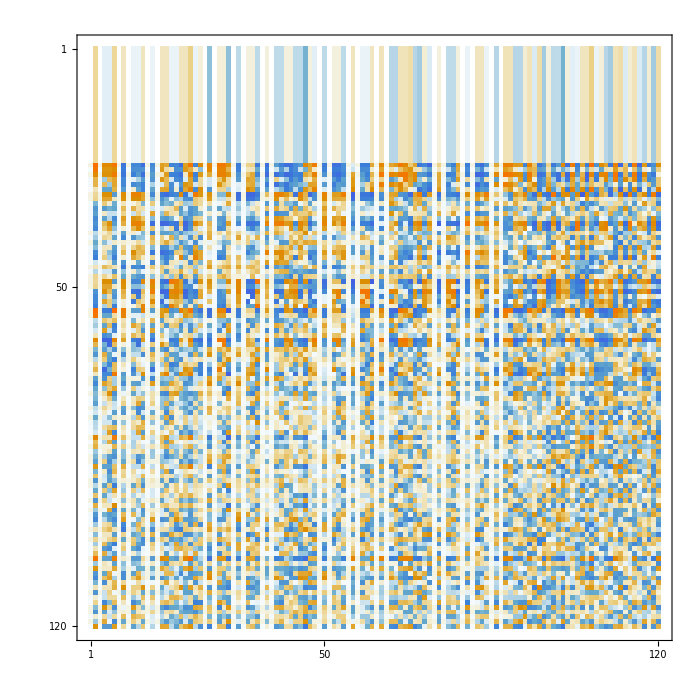

```mathematica
MatrixPlot@A
```